```mathematica
urbpop = FiltRegInd["SP.URB.TOTL"];
rurpop = FiltRegInd["SP.RUR.TOTL"];
totpop = FiltRegInd["SP.POP.TOTL"];

sumtotalregion[data_]:=Module[{},
 Table[Total@@(Replace[#,Except[_?NumberQ]-> 0,{1}]& /@{data[[reg,All,ano]]}),{reg,1,6},{ano,7,Length[data[[1,1]]]}]
]
```

```mathematica
ListPlot[{sumtotalregion[urbpop][[3]],sumtotalregion[rurpop][[3]]},{PlotLabels->{"Urban","Rural"},DataRange->{1960,2050},PlotLabel->"LAC",Joined->True, Filling->Axis}]
```

-Graphics-

```mathematica
urbf = ListInterpolation[
sumtotalregion[urbpop][[3]],{{1960,2050}}]
rurf =  ListInterpolation[
sumtotalregion[rurpop][[3]],{{1960,2050}}]
```

InterpolatingFunction[…]

InterpolatingFunction[…]

```mathematica
Plot[{urbf[x],rurf[x]},{x,1960,2100},{PlotLabel->"LAC",PlotLabels->{"Urban","Rural"},Filling->Axis}]
```

-Graphics-

```mathematica
maxyear[data_,region_,country_]:=Module[{f,x},
f=ListInterpolation[totpop[[region,country,7;;]],{1960,2050}];
x/.Last[FindMaximum[{f[x],1960≤ x ≤ 2150},{x,1960}]]
]
```

```mathematica
maxyears=Table[{totpop[[3,i,4]],maxyear[totpop,3,i]},{i,1,totpop[[3]]//Length}]
```

InterpolatingFunction::dmval: Input value {1959.99} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {2135.} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

FindMaximum::cvmit: Failed to converge to the requested accuracy or precision within 500 iterations.

FindMaximum::nrnum: The function value 0.- is not a real number at {x$292228} = {1960.}.

IPOPTMinimize::badobj: Invalid objective function. The objective function doesn't evaluate to a real-valued numeric result at the initial point.

FindMaximum::nrnum: The function value 0.- is not a real number at {x$292228} = {1959.99}.

General::stop: Further output of FindMaximum::nrnum will be suppressed during this calculation.

FindMaximum::grad: Evaluation of the gradient of function Experimental`NumericalFunction[{Hold[-«1»],Block},{0,{{{},1,0,Hold[x$292228],0,0}}},{{{1,1,817},{{Automatic,Automatic,None,2,Automatic},{}}}},«1»,{904,MachinePrecision,{{Automatic},{Hold[-«1»],Block}},True,{{Automatic,CleanUpRegisters→False,WarningMessages→False,EvaluateSymbolically→False,RuntimeErrorHandler→($Failed&)},{},Automatic,WVM},FindMaximum,Automatic,None},{None,None,None}] failed at {1960.}.

ReplaceAll::reps: {x$292228,1960} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindMaximum::cvmit: Failed to converge to the requested accuracy or precision within 500 iterations.

ReplaceAll::reps: {x$292634,1960} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

{{ATG,1979.2},{ARG,2060.95},{ABW,2037.89},{BHS,2150.},{BRB,2150.},{BLZ,2150.},{BOL,2087.5},{BRA,2047.35},{VGB,2049.54},{CYM,2044.21},{CHL,2053.5},{COL,2045.81},{CRI,2055.5},{CUB,2025.47},{CUW,1971.67},{DMA,1980.7},{DOM,2054.5},{ECU,2058.34},{SLV,2047.5},{GRD,1966.95},{GTM,2060.18},{GUY,1981.25},{HTI,2063.83},{HND,2150.},{JAM,2026.42},{MEX,2063.28},{NIC,2150.},{PAN,2150.},{PRY,2055.85},{PER,2057.87},{PRI,2003.72},{SXM,x$292228/.{x$292228,1960}},{KNA,1960.49},{LCA,2039.58},{MAF,x$292634/.{x$292634,1960}},{VCT,2020.42},{SUR,2150.},{TTO,2024.58},{TCA,1961.48},{URY,2048.58},{VEN,2061.01},{VIR,1999.96}}

```mathematica
BarChart[maxyears[[;;,2]],PlotRange->{1960,2100},ChartLegends->maxyears[[;;,1]]]
```

ReplaceAll::reps: {x$292228,1960.} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {x$292634,1960.} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {x$292228,1960.} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

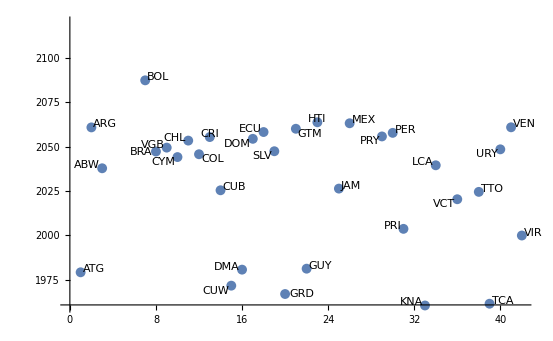

```mathematica
ListPlot[Table[Labeled[maxyears[[i,2]],maxyears[[i,1]]],{i,1,maxyears//Length}],PlotRange->{1960,2120}]
```